## Brian — PS 8 — 2025-02-18 — Solution

## EIWL3 Sections 20, 21, and 22

## Exercises from EIWL3 Section 20

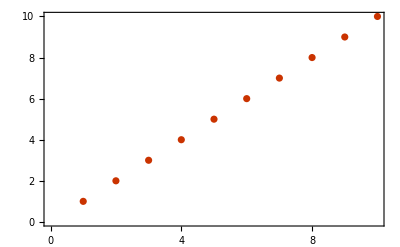

```mathematica
(* 20.1 *) ListPlot[Range[10], PlotTheme->"Web"]
```

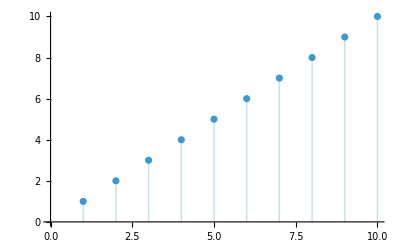

```mathematica
(* 20.2 *) ListPlot[Range[10],Filling->Axis]
(* That is interesting filling. I wonder if *)
(* Wolfram wanted a list line plot. *)
```

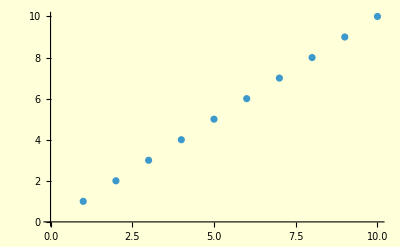

```mathematica
(* 20.3 *) ListPlot[Range[10],Background->LightYellow]
(* I couldn't bear the bright yellow so I dimmed it. *)
```

```mathematica
(* 20.4 *) GeoListPlot[Entity["Country","Australia"],GeoRange->All]
```

-Graphics-

```mathematica
(* 20.5 *) GeoListPlot[Entity["Country","Madagascar"],GeoRange->Entity["Ocean","IndianOcean"]]
```

-Graphics-

```mathematica
(* 20.6 *) GeoGraphics[EntityClass["Country","SouthAmerica"],GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
(* 20.7 *) GeoListPlot[{,Entity["Country","Finland"],},GeoRange->Entity["GeographicRegion","Europe"],GeoLabels->True]
```

-Graphics-

```mathematica
(* 20.8 *) GeoListPlot[EntityClass["University","TheIvyLeague"],GeoLabels->True]
```

-Graphics-

```mathematica
(* 20.9 *)Style[Grid[ Table[x y,{x,12},{y,12} ],Background->Black],White]
(* Is this the way we were meant to solve this? Well it works. *)
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
(* 20.10 *) Table[Graphics[Disk[],ImageSize->RandomInteger[{1,40}]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

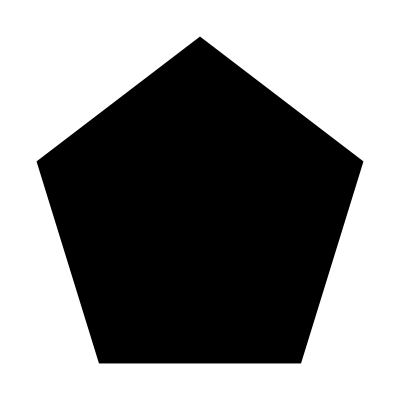
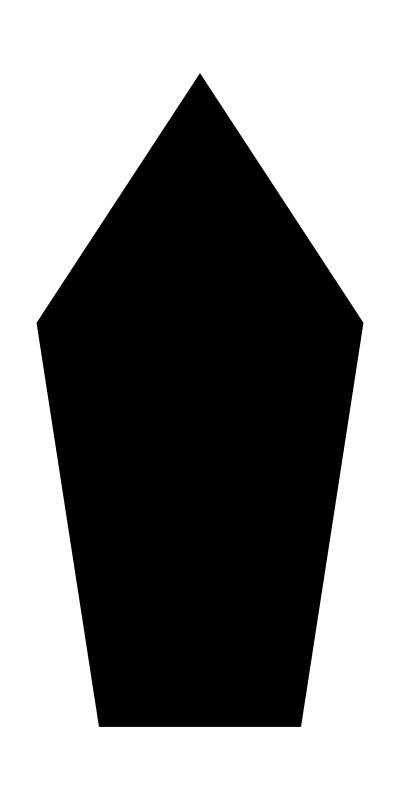
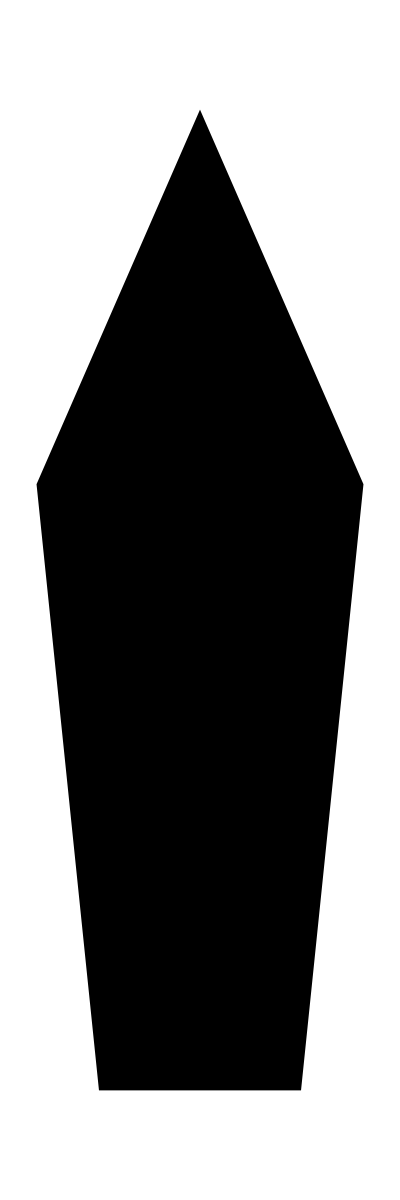
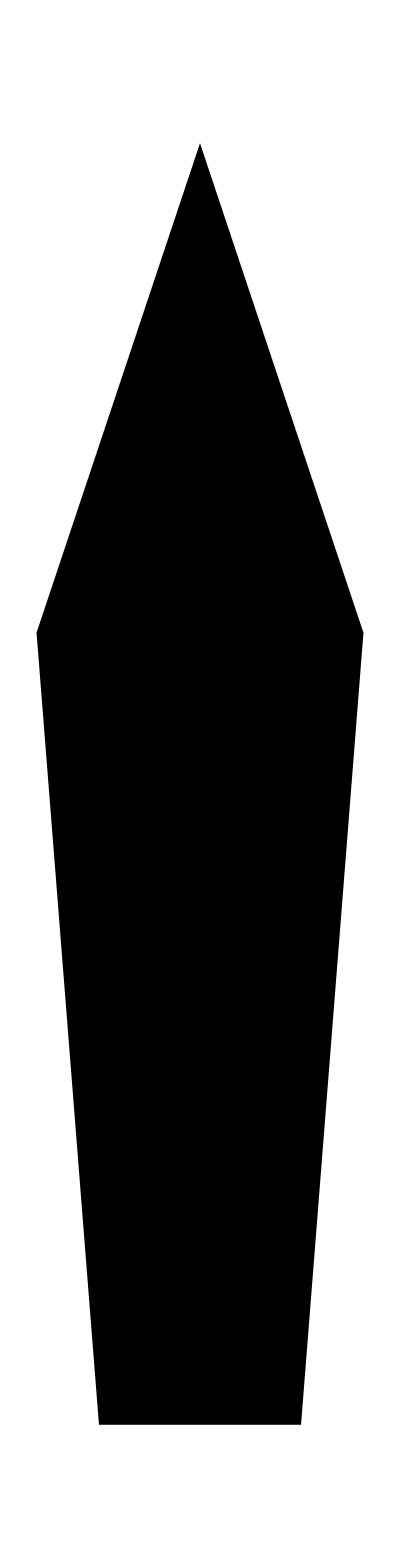
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 20.11 *) Table[Graphics[RegularPolygon[5],AspectRatio->aspectRatio],{aspectRatio,1,10}]
```

```mathematica
(* 20.12 *) Manipulate[Graphics[Circle[],ImageSize->size],{size,5,500}]
```

```mathematica
(* 20.13 *) Grid[Table[RandomColor[],{i,10},{j,10}],Frame->All]
```

RGBColor[0.8591340345369882, 0.46104051026762227, 0.2597260914625772] | RGBColor[0.2127270088656794, 0.8131913180602366, 0.11292474957402843] | RGBColor[0.3540573673768872, 0.5933004868774745, 0.7754042365206517] | RGBColor[0.5253313334122638, 0.39355348440682314, 0.1742626052294376] | RGBColor[0.748840841742997, 0.008245212965854343, 0.03420408331409486] | RGBColor[0.8185187426244223, 0.022336844729247574, 0.6380553945029259] | RGBColor[0.10797746299856881, 0.5465791181269379, 0.8478706722060312] | RGBColor[0.598874118678179, 0.3639694339687931, 0.6691049352424008] | RGBColor[0.6910981895897252, 0.9359691769470015, 0.07890140770034604] | RGBColor[0.39533110235351887, 0.4779929952307298, 0.8145675833106463]
RGBColor[0.7009417705209935, 0.28568120935950425, 0.851871593220781] | RGBColor[0.9014430123491421, 0.2720626556000254, 0.06409063457410524] | RGBColor[0.46554728580289795, 0.5677428584128523, 0.8706955040117945] | RGBColor[0.9651422102840026, 0.9163228843863866, 0.5260845731783244] | RGBColor[0.852696747266178, 0.35356511535274504, 0.06690196515912405] | RGBColor[0.9463519480788671, 0.5427060515736613, 0.6625456039813482] | RGBColor[0.6208587885298518, 0.4959212249032152, 0.15000308876923096] | RGBColor[0.604054912680686, 0.21578900208095697, 0.04192428442137652] | RGBColor[0.356789928543668, 0.04832180507898043, 0.8202354937058691] | RGBColor[0.8602649904938855, 0.3131155314514198, 0.558391460983672]
RGBColor[0.2073780335053117, 0.0870369000114819, 0.5847103367321711] | RGBColor[0.9900404797122873, 0.7350255541787376, 0.7426313890435308] | RGBColor[0.54928428081424, 0.5869563875455786, 0.2781580615456718] | RGBColor[0.5642791521708939, 0.6623491943863098, 0.10946660557104781] | RGBColor[0.909315877499604, 0.2762856712579569, 0.8581962989896668] | RGBColor[0.7925628344509583, 0.18153824505874394, 0.6414357658434038] | RGBColor[0.6437837301311697, 0.3586293467047421, 0.9970975961018071] | RGBColor[0.6557642580540377, 0.9232842085210429, 0.4432540297195715] | RGBColor[0.1996693306988857, 0.9177511172771595, 0.3966640079410686] | RGBColor[0.6189821534251194, 0.7235836973279461, 0.7991917857641211]
RGBColor[0.25493731283159193, 0.07771154298268113, 0.9176805980907607] | RGBColor[0.17017272513707482, 0.3273346680339262, 0.8563456115157513] | RGBColor[0.2878657549319905, 0.28165242859872364, 0.02284395054098365] | RGBColor[0.2570802111511974, 0.6935580762118305, 0.42423128365581464] | RGBColor[0.6070153802980793, 0.2794473379529616, 0.04347239308923667] | RGBColor[0.287135540262619, 0.25085193240186543, 0.0490394811351027] | RGBColor[0.9153569930438177, 0.4412665369923163, 0.8440325584700838] | RGBColor[0.7785251137444094, 0.7524354640796611, 0.04344786376781773] | RGBColor[0.02885057771566668, 0.45686615841433054, 0.06728479132786958] | RGBColor[0.5162234054952073, 0.8596238132431706, 0.38747396436294657]
RGBColor[0.9712511512586852, 0.7538088639111502, 0.6973212419575754] | RGBColor[0.3350187118555177, 0.5976884187001843, 0.3602573166271552] | RGBColor[0.3577820860841503, 0.4487529981134841, 0.8497300129922607] | RGBColor[0.4682121448954284, 0.6367616193189323, 0.21847463427472147] | RGBColor[0.4952832806341836, 0.06301454454723898, 0.3707714910008515] | RGBColor[0.09959458521749953, 0.9173037223660738, 0.9483160697752842] | RGBColor[0.8802960038314251, 0.9016519276081951, 0.4224390707895129] | RGBColor[0.9814869123324421, 0.7791320954223899, 0.16253575888332872] | RGBColor[0.7862714611109485, 0.03770411341469493, 0.49682708898465977] | RGBColor[0.9373052309965428, 0.24248523320829163, 0.49237893128373766]
RGBColor[0.39957658677857877, 0.2587463962443821, 0.8552266713634078] | RGBColor[0.7557694362937768, 0.29730215677093685, 0.3540010639952671] | RGBColor[0.8276819395441335, 0.11418668920271702, 0.08344464272542118] | RGBColor[0.6535431724641796, 0.5747725902951046, 0.06040083929482121] | RGBColor[0.3210967705432526, 0.1385935178916211, 0.24379777401567715] | RGBColor[0.14965309136811178, 0.3516818654568359, 0.8107315124313468] | RGBColor[0.09156610370569718, 0.8087267499029458, 0.5512418928328979] | RGBColor[0.8500671884523985, 0.5071250912823062, 0.3327994800837284] | RGBColor[0.36866101955379893, 0.095614590969884, 0.4742686943565373] | RGBColor[0.6947776573524989, 0.03358121921898527, 0.2699042419763795]
RGBColor[0.7084377400377875, 0.21136473259774724, 0.7766338797955248] | RGBColor[0.7438174490074536, 0.7145293192809896, 0.40892281066707103] | RGBColor[0.9011149231241822, 0.684407999640456, 0.29260925024252527] | RGBColor[0.7175746031742949, 0.9969159170484483, 0.23421029763958678] | RGBColor[0.270658409271582, 0.5435123316981694, 0.01681046178949286] | RGBColor[0.9867794351152686, 0.5731184792209845, 0.475084909124299] | RGBColor[0.454871120313016, 0.25247315135703974, 0.9628098041880104] | RGBColor[0.1321602806622375, 0.33004134797975704, 0.7147438085394] | RGBColor[0.8112259768653576, 0.33034852609231136, 0.7345323013218883] | RGBColor[0.45632073404951456, 0.13629600377907414, 0.18010216556583414]
RGBColor[0.4324501311118567, 0.9181492680520245, 0.90427558970878] | RGBColor[0.12250362626868383, 0.39388256173557346, 0.5988327822889778] | RGBColor[0.8350598688183901, 0.6313920351461366, 0.8131982119753411] | RGBColor[0.5188914593103706, 0.053804219962789945, 0.96884935814052] | RGBColor[0.08422378868674962, 0.1663036191901468, 0.4390686936265664] | RGBColor[0.9483079236499907, 0.1713471841148233, 0.7332096927661291] | RGBColor[0.17621902853162097, 0.6002607678452649, 0.6807537256775054] | RGBColor[0.18633709104919927, 0.6221572586922699, 0.5237572335936946] | RGBColor[0.5552603358795949, 0.6250116079311661, 0.5053514426973378] | RGBColor[0.01310061501531945, 0.9097040285963751, 0.4528835977137]
RGBColor[0.4476516164408266, 0.10418729663920234, 0.37742236754323555] | RGBColor[0.9885872018111495, 0.6650199727444399, 0.14608862687088608] | RGBColor[0.03960513052301606, 0.23074799616620667, 0.6912821204879962] | RGBColor[0.9324448310236342, 0.668800849503641, 0.2019575898782926] | RGBColor[0.09250279545714246, 0.7613517921068309, 0.015055415209856982] | RGBColor[0.7990559745242818, 0.8505086504291275, 0.9522306616828953] | RGBColor[0.3969942036520313, 0.42205147148030275, 0.12998009432214075] | RGBColor[0.37012501682177334, 0.3289785774590088, 0.8855284786387378] | RGBColor[0.80174583108258, 0.9958037276238971, 0.3451492394372675] | RGBColor[0.08226299682434912, 0.4428941018634116, 0.8711575410851113]
RGBColor[0.23045503614740181, 0.019902653633030898, 0.19276106201515408] | RGBColor[0.020655724192811586, 0.29750021668666715, 0.0732919851756404] | RGBColor[0.1114564916980132, 0.03880860746739345, 0.29672992956465816] | RGBColor[0.5701899045010639, 0.7046954575305777, 0.011424251229647409] | RGBColor[0.6053972553879259, 0.13172691196974307, 0.5380989572766841] | RGBColor[0.023506823954459133, 0.8610998267411667, 0.6732261458539834] | RGBColor[0.2936203610386323, 0.760194758257462, 0.9586462283687194] | RGBColor[0.38271109616652366, 0.8786976180881279, 0.5247010670673222] | RGBColor[0.21522407871803395, 0.26053672351353696, 0.628873467840021] | RGBColor[0.5337011923613797, 0.7298218678913206, 0.48204385888666623]

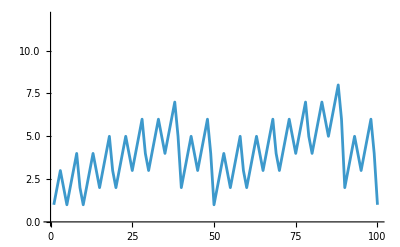

```mathematica
(* 20.24 *) ListLinePlot[
Table[StringLength[RomanNumeral[i]],{i,100}],
PlotRange->Max[Table[StringLength[RomanNumeral[i]],{i,1000}]]]
```

## Exercises from EIWL3 Section 21

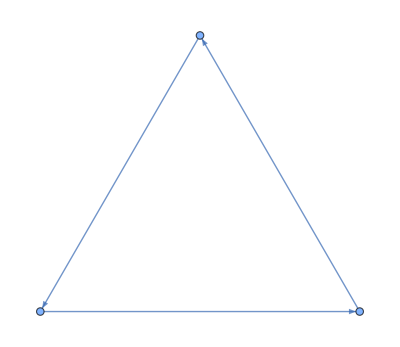

```mathematica
(* 21.1 *) Graph[{1->2,2->3,3->1}]
```

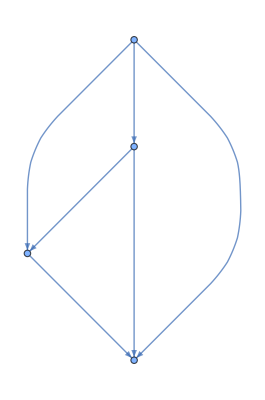

```mathematica
(* 21.2 *) Graph[{1->2,1->3,1->4,2->3,2->4,3->4}]
```

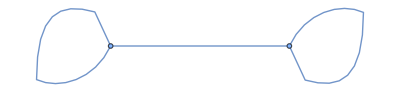
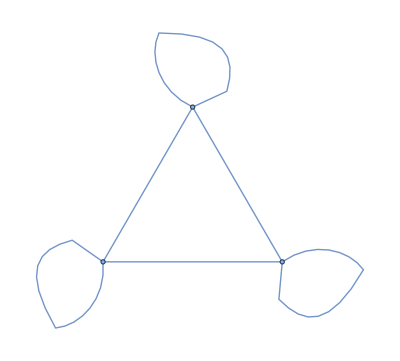
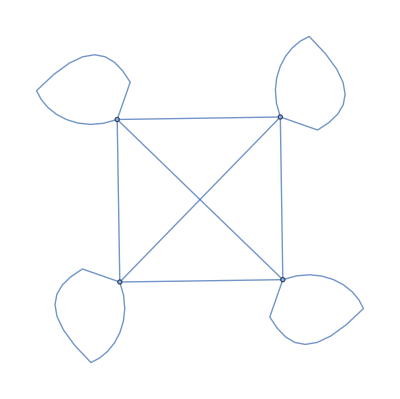
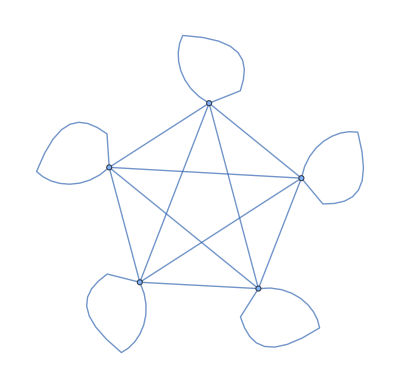
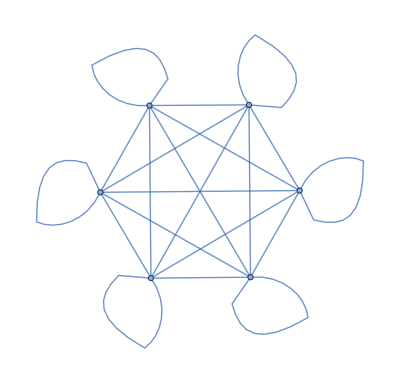
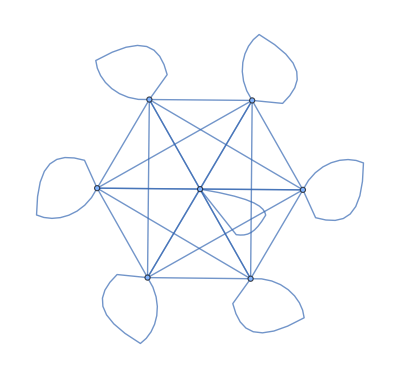
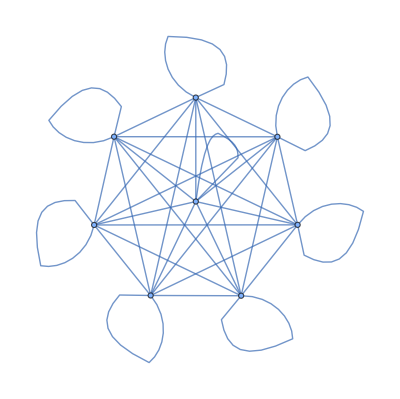
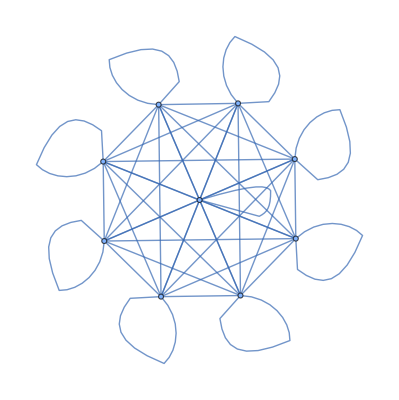

```mathematica
(* 21.3 *) Table[UndirectedGraph[Flatten[Table[i->j,{i,nodes},{j,nodes}]]],{nodes,2,10}]
```

```mathematica
(* 21.4 *) Flatten[Table[i,3,{i,2}]]
```

{1,2,1,2,1,2}

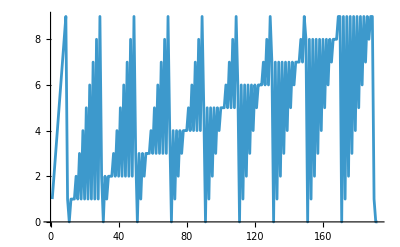

```mathematica
(* 21.5 *) ListLinePlot[Flatten[Table[IntegerDigits[number],{number, 100}]]]
```

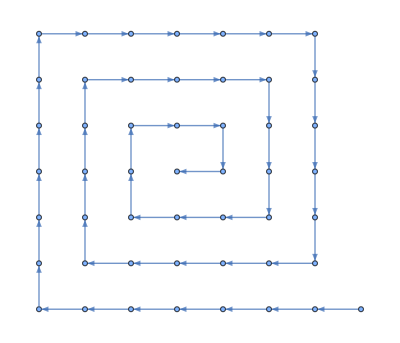

```mathematica
(* 21.6 *) Graph[Table[i->i+1,{i,1,49}]]
```

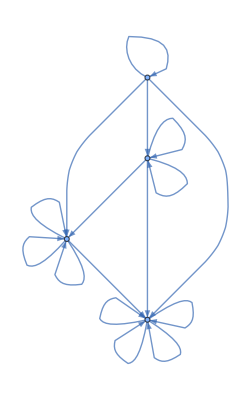

```mathematica
(* 21.7 *) Graph[Flatten[Table[i->Max[i,j],{i,4},{j,4}]]]
```

```mathematica
(* 21.8 *) Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

```mathematica
(* 21.9 *) Graph[Table[i->RandomInteger[{1,100}],{i,100}]]
```

-Graphics-

```mathematica
(* 21.10 *) Graph[Flatten[Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,100}]]]
```

-Graphics-

```mathematica
(* 21.11 *) Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],i,j],{i,4},{j,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

## Exercises from EIWL3 Section 22

```mathematica
(* 22.1 *) LanguageIdentify["ajatella"]
```

Finnish

```mathematica
(* This will be useful in the next two exercises: *)
tigerImage=Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]];
```

```mathematica
(* 22.2 *) ImageIdentify[tigerImage]
```

tiger

```mathematica
(* 22.3 *) 
ImageIdentify[Table[Blur[tigerImage,blur],{blur,5}]]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
(* 22.4 *) Classify["Sentiment", "I'm so happy to be here"]
```

Positive

```mathematica
(* 22.5 *) Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
(* 22.6 *) Nearest[RandomInteger[1000,20],100,3]
```

{132,6,203}

```mathematica
(* 22.7 *) Nearest[RandomColor[10],Red,5]
```

{RGBColor[0.8061409889140809, 0.7470027443315164, 0.11557484494886872],RGBColor[0.46538118808127193, 0.3787542257795047, 0.6267047314844214],RGBColor[0.3492391208823198, 0.5960786347778908, 0.38977792229936425],RGBColor[0.47714968063623364, 0.7854707341159624, 0.16435961396697807],RGBColor[0.10496502182086731, 0.6546109037447903, 0.34382946005386295]}

```mathematica
(* 22.8 *) Nearest[Range[100]^2,2000]
```

{2025}

```mathematica
(* 22.9 *) Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

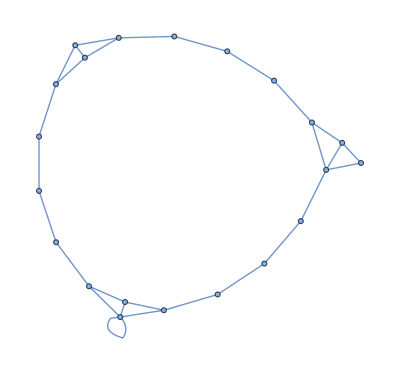

```mathematica
(* 22.10 *) NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2]
```

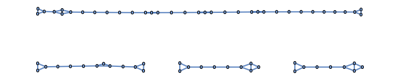

```mathematica
(* 22.11 *) NearestNeighborGraph[RandomInteger[100,100],2]
```


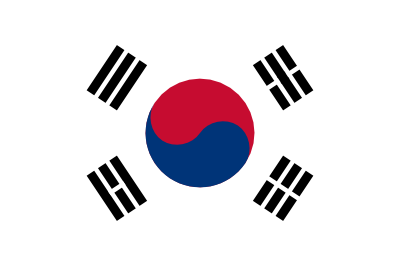
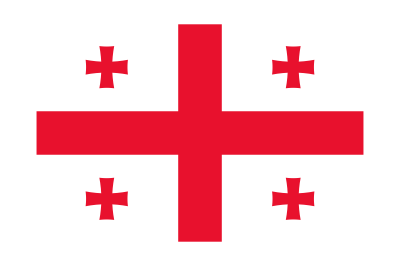
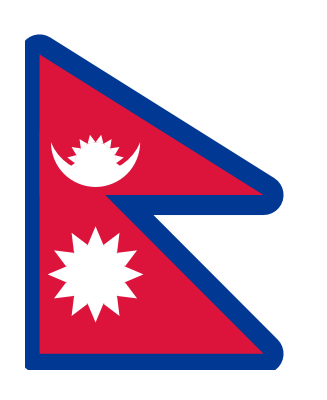
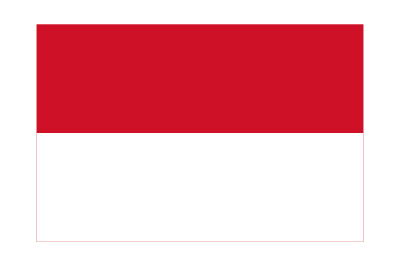
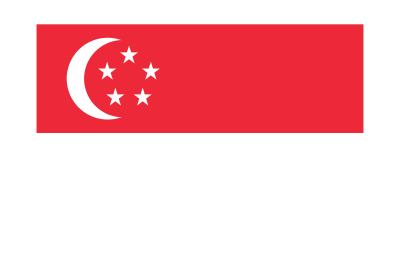
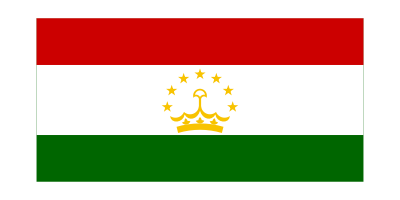
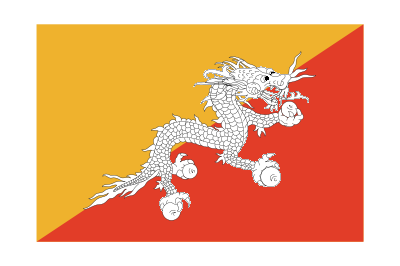
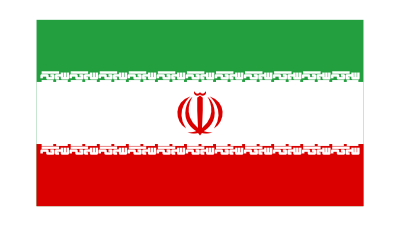

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
(* 22.12 *) FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
(* 22.13 *) Table[Rasterize[letter,RasterSize->20],{letter,Alphabet[]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

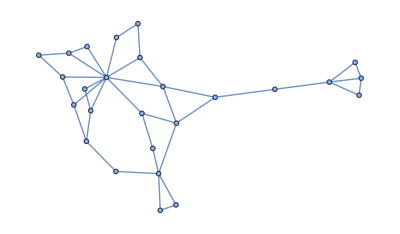

```mathematica
NearestNeighborGraph[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2]
```